## Our problem statement

In a Cartesian plane, consider two distinct sets of points denoted as A and B. Set A exclusively consists of points located along the X-axis, serving as a reflective plane mirror. Conversely, set B comprises points positioned along an unknown, arbitrary reflective curve represented by f(x). These points represent the locations where a ray of light, originating from the origin and striking point P (which belongs to set B), undergoes successive reflections. Given this configuration, determine nature of the reflective curve f(x).

Equation Of Reflective Curve In Parametric and Cartesian Form

```mathematica
curveparaeqn = {8t, -2 t^2+6}
curvecarteqn = Last[List @@ Reduce[Eliminate[{curveparaeqn[[1]]==x,curveparaeqn[[2]]==y}, t],y]]
```

{8 t,6-2 t^2}

1/32 (192-x^2)

Plot of the equation

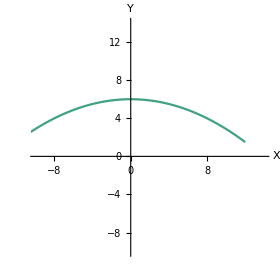

```mathematica
curve = ParametricPlot[curveparaeqn, {t, -1.5, 1.5},PlotRange->{-10, 14},AxesLabel->{"X", "Y"},AxesStyle->Arrowheads[.02], ColorFunction->"BlueGreenYellow"]
```

Incident ray of light at 45 degrees to x axis with source at origin

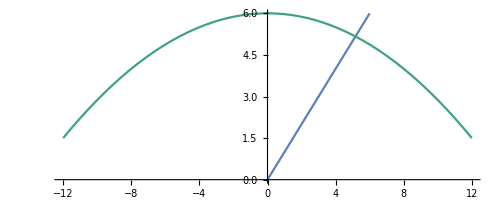

{{5.16601,5.16601}}

```mathematica
sourceparaeqn = {t, t};
sourcecarteqn = x;
sourceline = ParametricPlot[sourceparaeqn, {t, 0, 6}, PlotRange->All];
Show[sourceline, curve]
ptlist = {};
ptlist = AppendTo[ptlist, {x /. N[Solve[sourcecarteqn==curvecarteqn, x]][[2]] , curvecarteqn /. N[Solve[sourcecarteqn==curvecarteqn, x]][[2]]}]
```

Functions for reflection angles and equations

```mathematica
curverefangle[incipt_,prevrefangle_]:= 
	Reduce[(prevrefangle-(-1/(D[curvecarteqn, x] /. {x->incipt[[1]]})))/(1+prevrefangle*(-1/(D[curvecarteqn, x] /.{x->incipt[[1]]})))
		== ((-1/(D[curvecarteqn, x] /.{x->incipt[[1]]}))-m)/(1+(-1/(D[curvecarteqn, x] /.{x->incipt[[1]]}))*m),m];
		
curverefeqn[incipt_, refangle_]:=  Reduce[y-(curvecarteqn /. {x->incipt[[1]]} )== Last[List @@ refangle](x-({x} /. {x->incipt[[1]]})[[1]]),y];

plincipt[refeqn_] := {x /. Solve[refeqn /. y->0][[1]][[1]], 0};

plrefeqn[incipt_, angle_] := Last[List @@ Reduce[y-0==-Last[List @@ angle](x-incipt[[1]]),y]];

curveinci[plrefeqn_] := Module[{b},
								For[z = N[Solve[plrefeqn==curvecarteqn, x]]; i=0, i<Length[a], i++;
								If[(x /. z[[i]])>-10 && (x /. z[[i]])<10 , b = {x /. z[[i]], curvecarteqn /. z[[i]]}]];
								b]
```

```mathematica
eqnlist = {};
ptlist = {{0,0},{5.166010488516726,5.166010488516724}};
mergefunction[list_] := Module[{},
						 a = curverefangle[list[[1]], list[[2]]];
						 b = curverefeqn[list[[1]],a];
						 c = plincipt[curverefeqn[list[[1]],a]];
						 d = plrefeqn[c, a];
						 e = curveinci[d];
						eqnlist = AppendTo[eqnlist, {Last[List @@b],d}];
						ptlist = AppendTo[ptlist, c];
						ptlist = AppendTo[ptlist, e];
						z = {e,-Last[List @@ a]};
						z]
```

```mathematica
Nest[mergefunction,{{5.166010488516726,5.166010488516724}, 1} , 6]
eqnlist;
ptlist;
```

```mathematica
p1 = ptlist
Length[p1]
Export["C:\\Users\\PC\\Desktop\\PINN\\Python\\test14.csv",p1, "CSV"]
```

{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-5.43523,0},{-3.67879,5.57708},{1.59124,0},{6.14562,4.81973},{6.25961,0},{6.37152,4.73137}}

14

C:\Users\PC\Desktop\PINN\Python\test14.csv

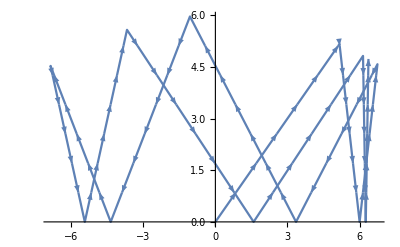

```mathematica
z2 = ListLinePlot[p1, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

12 reflection pairs after first incident

```mathematica
Nest[mergefunction,{{5.166010488516726,5.166010488516724}, 1} , 12]
eqnlist;
ptlist;
```

{{-4.70059,5.30951},-1.00704}

```mathematica
ptlist2 = ptlist
Length[ptlist2]
Export["C:\\Users\\PC\\Desktop\\PINN\\Python\\test2.csv",ptlist2, "CSV"]
```

{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-5.43523,0},{-3.67879,5.57708},{1.59124,0},{6.14562,4.81973},{6.25961,0},{6.37152,4.73137},{2.1006,0},{-3.05262,5.7088},{-5.18351,0},{-6.87221,4.52415},{-4.66373,0},{-1.78332,5.90062},{2.95058,0},{6.65413,4.61633},{6.13436,0},{5.56788,5.03121},{0.571821,0},{-4.70059,5.30951}}

26

C:\Users\PC\Desktop\PINN\Python\test2.csv

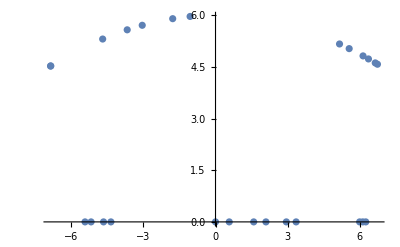

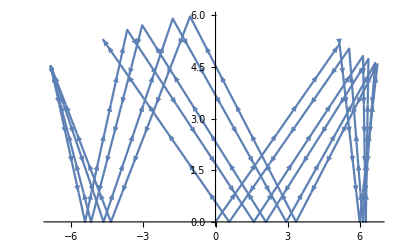

```mathematica
z1 = ListPlot[ptlist]
z2 = ListLinePlot[ptlist, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

## Valid Path Formations

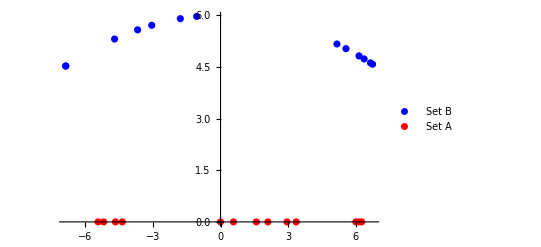

```mathematica
intersecpts = ptlist;
For[xaxispts = {}; i=0, i<Length[intersecpts], i++; If[intersecpts[[i, 2]]==0, AppendTo[xaxispts, intersecpts[[i]]]]]
curvepts = Sort[DeleteCases[intersecpts, Alternatives @@ xaxispts]];
xaxispts = Sort[xaxispts];
sepplot = ListPlot[{curvepts, xaxispts}, PlotStyle->{Blue, Red},PlotLegends->{"Set B", "Set A"}]
```

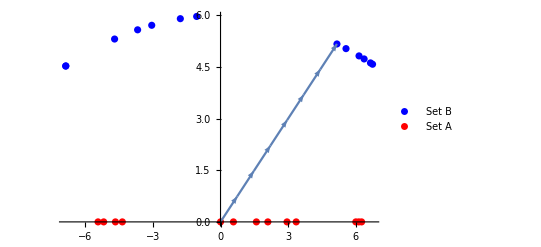

```mathematica
z1 = ListLinePlot[{{0,0},{5.166010488516726,5.166010488516724}},Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow;
Show[sepplot,z1 ]
```

```mathematica
Clear[i, j, k]
reflecpathls = {};
For[i=0, i<Length[xaxispts], i++;
	For[j=0, j<Length[curvepts], j++;
		For[k=0, k<Length[curvepts], k++;
			If[curvepts[[j]]==curvepts[[k]], Continue[]];
			If[(curvepts[[k]][[2]]-xaxispts[[i]][[2]])/(curvepts[[k]][[1]]-xaxispts[[i]][[1]]) == -(curvepts[[j]][[2]]-xaxispts[[i]][[2]])/(curvepts[[j]][[1]]-xaxispts[[i]][[1]]), 
				reflecpathls = AppendTo[reflecpathls, {curvepts[[k]], xaxispts[[i]], curvepts[[j]]}]]]]]
reflecpathls;
```

```mathematica
reversepathls = {};
For[i=0, i<Length[reflecpathls], i++;
	reversepathls = AppendTo[reversepathls, Reverse[reflecpathls[[i]]]]]
reversepathls;
```

```mathematica
legalpaths = Join[reflecpathls , reversepathls];
```

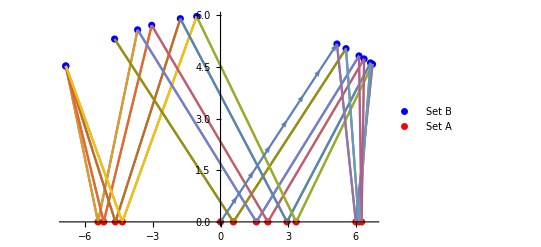

```mathematica
Show[sepplot, ListLinePlot[reflecpathls], z1]
```

20 reflection pairs after first incident

```mathematica
eqnlist = {};
ptlist = {{0,0},{5.166010488516726,5.166010488516724}};
Nest[mergefunction,{{5.166010488516726,5.166010488516724}, 1} , 15]
eqnlist;
ptlist;
```

{{6.83924,4.53828},1.61563}

```mathematica
ptlist3 = ptlist
Length[ptlist3]
Export["C:\\Users\\PC\\Desktop\\PINN\\Python\\test3.csv",ptlist3, "CSV"]
```

{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-5.43523,0},{-3.67879,5.57708},{1.59124,0},{6.14562,4.81973},{6.25961,0},{6.37152,4.73137},{2.1006,0},{-3.05262,5.7088},{-5.18351,0},{-6.87221,4.52415},{-4.66373,0},{-1.78332,5.90062},{2.95058,0},{6.65413,4.61633},{6.13436,0},{5.56788,5.03121},{0.571821,0},{-4.70059,5.30951},{-5.83448,0},{-6.80664,4.55218},{-3.73195,0},{0.318495,5.99683},{4.03025,0},{6.83924,4.53828}}

32

C:\Users\PC\Desktop\PINN\Python\test3.csv

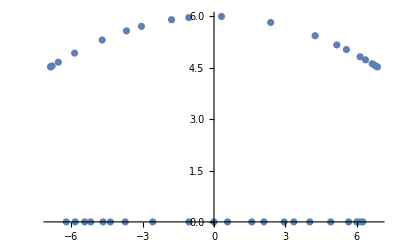

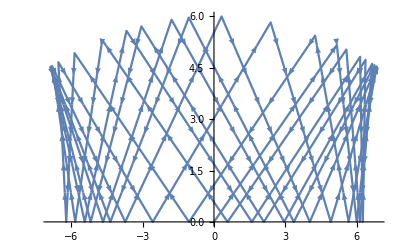

```mathematica
z1 = ListPlot[ptlist]
z2 = ListLinePlot[ptlist, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

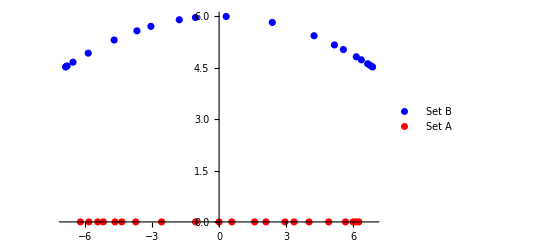

```mathematica
intersecpts = ptlist;
For[xaxispts = {}; i=0, i<Length[intersecpts], i++; If[intersecpts[[i, 2]]==0, AppendTo[xaxispts, intersecpts[[i]]]]]
curvepts = Sort[DeleteCases[intersecpts, Alternatives @@ xaxispts]];
xaxispts = Sort[xaxispts];
sepplot = ListPlot[{curvepts, xaxispts}, PlotStyle->{Blue, Red},PlotLegends->{"Set B", "Set A"}]
```

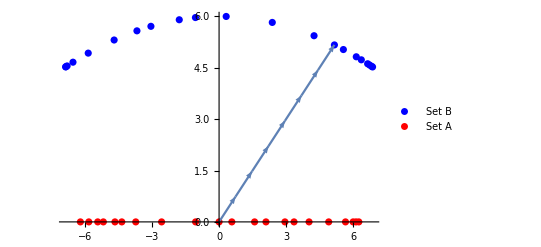

```mathematica
z1 = ListLinePlot[{{0,0},{5.166010488516726,5.166010488516724}},Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow;
Show[sepplot,z1 ]
```

```mathematica
Clear[i, j, k]
reflecpathls = {};
For[i=0, i<Length[xaxispts], i++;
	For[j=0, j<Length[curvepts], j++;
		For[k=0, k<Length[curvepts], k++;
			If[curvepts[[j]]==curvepts[[k]], Continue[]];
			If[(curvepts[[k]][[2]]-xaxispts[[i]][[2]])/(curvepts[[k]][[1]]-xaxispts[[i]][[1]]) == -(curvepts[[j]][[2]]-xaxispts[[i]][[2]])/(curvepts[[j]][[1]]-xaxispts[[i]][[1]]), 
				reflecpathls = AppendTo[reflecpathls, {curvepts[[k]], xaxispts[[i]], curvepts[[j]]}]]]]]
reflecpathls;
```

```mathematica
reversepathls = {};
For[i=0, i<Length[reflecpathls], i++;
	reversepathls = AppendTo[reversepathls, Reverse[reflecpathls[[i]]]]]
reversepathls;
```

```mathematica
legalpaths = Join[reflecpathls , reversepathls];
```

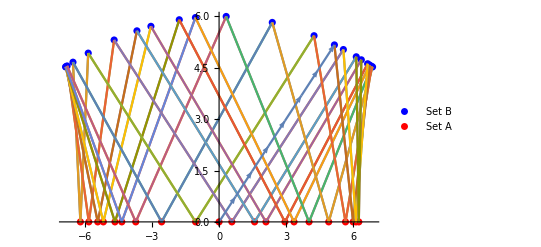

```mathematica
Show[sepplot, ListLinePlot[reflecpathls], z1]
```

100 reflection pairs after first incident

```mathematica
eqnlist = {};
ptlist = {{0,0},{5.166010488516726,5.166010488516724}};
Nest[mergefunction,{{5.166010488516726,5.166010488516724}, 1} , 100]
eqnlist;
ptlist;
```

{{-6.58482,4.645},-11.7439}

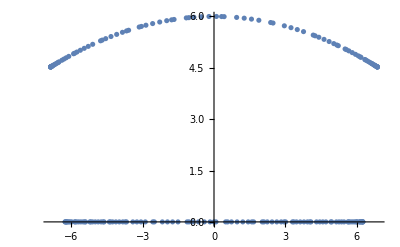

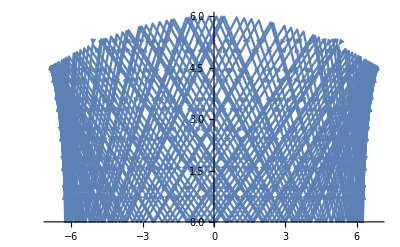

```mathematica
z1 = ListPlot[ptlist]
z2 = ListLinePlot[ptlist, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

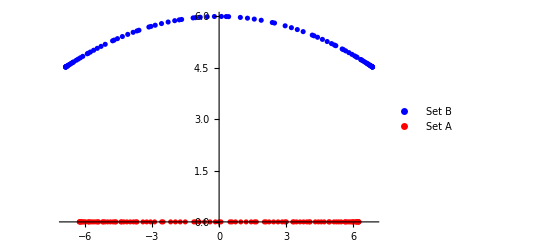

```mathematica
intersecpts = ptlist;
For[xaxispts = {}; i=0, i<Length[intersecpts], i++; If[intersecpts[[i, 2]]==0, AppendTo[xaxispts, intersecpts[[i]]]]]
curvepts = Sort[DeleteCases[intersecpts, Alternatives @@ xaxispts]];
xaxispts = Sort[xaxispts];
sepplot = ListPlot[{curvepts, xaxispts}, PlotStyle->{Blue, Red},PlotLegends->{"Set B", "Set A"}]
```

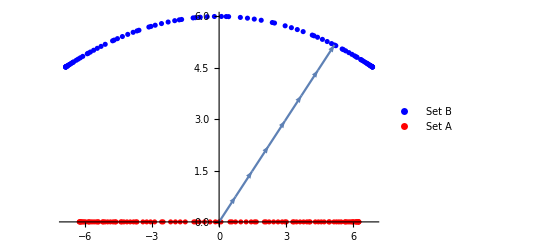

```mathematica
z1 = ListLinePlot[{{0,0},{5.166010488516726,5.166010488516724}},Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow;
Show[sepplot,z1 ]
```

```mathematica
Clear[i, j, k]
reflecpathls = {};
For[i=0, i<Length[xaxispts], i++;
	For[j=0, j<Length[curvepts], j++;
		For[k=0, k<Length[curvepts], k++;
			If[curvepts[[j]]==curvepts[[k]], Continue[]];
			If[(curvepts[[k]][[2]]-xaxispts[[i]][[2]])/(curvepts[[k]][[1]]-xaxispts[[i]][[1]]) == -(curvepts[[j]][[2]]-xaxispts[[i]][[2]])/(curvepts[[j]][[1]]-xaxispts[[i]][[1]]), 
				reflecpathls = AppendTo[reflecpathls, {curvepts[[k]], xaxispts[[i]], curvepts[[j]]}]]]]]
reflecpathls;
```

Paths with common point of beginning

```mathematica
samepts = {};
For[i=0, i<Length[reflecpathls], i++;
	For[j =0, j<Length[reflecpathls], j++;
		For[z = 0, z<Length[reflecpathls], z++;
			If[i!=j!=z && reflecpathls[[i]][[1]]== reflecpathls[[j]][[1]]==reflecpathls[[z]][[1]],samepts = AppendTo[samepts, Join[reflecpathls[[j]],reflecpathls[[i]]]]]]]]
Length[reflecpathls]
Length[samepts]
```

200

0

Zero common paths

```mathematica
reversepathls = {};
For[i=0, i<Length[reflecpathls], i++;
	reversepathls = AppendTo[reversepathls, Reverse[reflecpathls[[i]]]]]
reversepathls;
```

```mathematica
legalpaths = Join[reflecpathls , reversepathls];
```

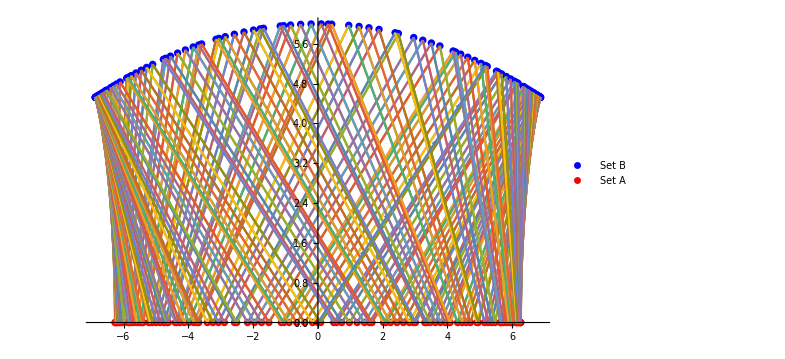

```mathematica
Show[sepplot, ListLinePlot[reflecpathls], z1]
```

300 reflection pairs after first incident

```mathematica
eqnlist = {};
ptlist = {{0,0},{5.166010488516726,5.166010488516724}};
Nest[mergefunction,{{5.166010488516726,5.166010488516724}, 1} , 300]
eqnlist;
ptlist;
```

{{6.84374,4.53635},3.7333}

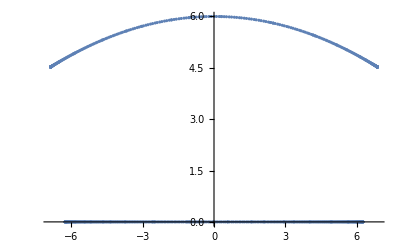

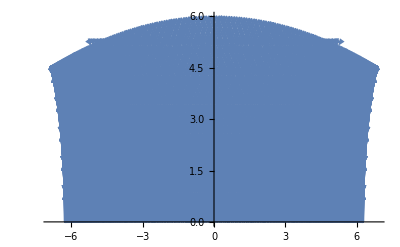

```mathematica
z1 = ListPlot[ptlist]
z2 = ListLinePlot[ptlist, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

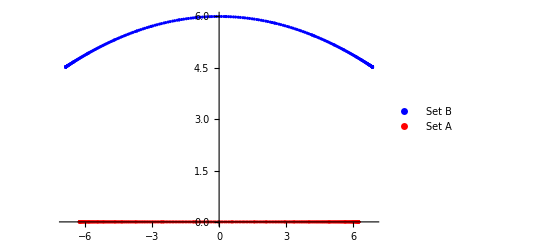

```mathematica
intersecpts = ptlist;
For[xaxispts = {}; i=0, i<Length[intersecpts], i++; If[intersecpts[[i, 2]]==0, AppendTo[xaxispts, intersecpts[[i]]]]]
curvepts = Sort[DeleteCases[intersecpts, Alternatives @@ xaxispts]];
xaxispts = Sort[xaxispts];
sepplot = ListPlot[{curvepts, xaxispts}, PlotStyle->{Blue, Red},PlotLegends->{"Set B", "Set A"}]
```

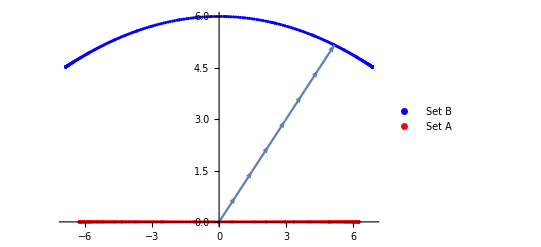

```mathematica
z1 = ListLinePlot[{{0,0},{5.166010488516726,5.166010488516724}},Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow;
Show[sepplot,z1 ]
```

```mathematica
Clear[i, j, k]
reflecpathls = {};
For[i=0, i<Length[xaxispts], i++;
	For[j=0, j<Length[curvepts], j++;
		For[k=0, k<Length[curvepts], k++;
			If[curvepts[[j]]==curvepts[[k]], Continue[]];
			If[(curvepts[[k]][[2]]-xaxispts[[i]][[2]])/(curvepts[[k]][[1]]-xaxispts[[i]][[1]]) == -(curvepts[[j]][[2]]-xaxispts[[i]][[2]])/(curvepts[[j]][[1]]-xaxispts[[i]][[1]]), 
				reflecpathls = AppendTo[reflecpathls, {curvepts[[k]], xaxispts[[i]], curvepts[[j]]}]]]]]
reflecpathls;
```

Path with common point of beginning

```mathematica
samepts = {};
For[i=0, i<Length[reflecpathls], i++;
	For[j =0, j<Length[reflecpathls], j++;
		For[z = 0, z<Length[reflecpathls], z++;
			If[i!=j!=z && reflecpathls[[i]][[1]]== reflecpathls[[j]][[1]]==reflecpathls[[z]][[1]],samepts = AppendTo[samepts, Join[reflecpathls[[j]],reflecpathls[[i]]]]]]]]
Length[reflecpathls]
Length[samepts]
```

$Aborted

596

0

```mathematica
reversepathls = {};
For[i=0, i<Length[reflecpathls], i++;
	reversepathls = AppendTo[reversepathls, Reverse[reflecpathls[[i]]]]]
reversepathls;
```

```mathematica
legalpaths = Join[reflecpathls , reversepathls];
```

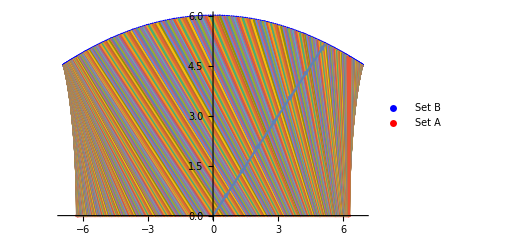

```mathematica
Show[sepplot, ListLinePlot[reflecpathls], z1]
```